## Mineralized Model Analysis of the SH0ES Measurement of H_0. Search for a transition is implemented. For different generalized parameters, the parameter ‘col’ needs to be changed and the table qpar1. The rest may even remain as they are (the range of the final plot may also need to be changed).

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];  
 Off[Inverse::luc];
```

## Matrix of Measurements Y- Matrix of Parameters q - Design Matrix L- Error Matrix C

```mathematica
cdata=Import[".\\data\\allc_shoes_ceph_topantheonwt6.0_112221.fits","RawData"];
ydata=Import[".\\data\\ally_shoes_ceph_topantheonwt6.0_112221.fits","RawData"] [[1]]//Normal;
ldata=Import[".\\data\\alll_shoes_ceph_topantheonwt6.0_112221.fits","RawData"]//Normal;
dist1=Import[".\\data\\dist.dat"]//Flatten;
```

```mathematica
dof=3446;
```

```mathematica
NN=3492;
MM=48;
```

```mathematica
maxdist=60; (* this is the maximum distance considered in do loop in Mpc that distinguishes nearby and distant objects/constraints in Y.  *)
mindist=1; (* this is the minimum distance considered in do loop in Mpc that distinguishes nearby and distant objects/constraints in Y.  *)
step=2; (* this is the distance step considered in do loop  *)

col=47-8; (* this column corresponds to the parameter to be split (e.g. for MW we have col=39) *)
qpar1={μ67,μ385,μ354,μ356,μ738,μ294,μ228,μ163,μ193,μ201,μ272,μ354,μ266,μ425,μ244,μ24,μ208,μ344,μ151,μ190,μ293,μ164,μ319,μ198,μ421,μ463,μ280,μ207,μ449,μ303,μ310,μ128,μ468,μ344,μ466,μ605,μ294,ΔμΝ4258,MWs,MWl,ΔμLMC,μM31,bW,MB,ZW,X,ΔZp,p5ogh0}; (* introduce here the names of the two new parameters that replace the previous parameter *)

Call=cdata[[1]]//Normal; (* Covariance matrix. This does not change since the Y matrix remained the same with no new constraints. *)
InvCall=Inverse[Call];
it=InvCall.Call//Chop;
zerot=it-IdentityMatrix[Length[it]]//Chop;
zerot[[1]];  (* test the inversion of Call due to the mathematica complaints. These are due to the parameter X introduced arbitrarily in the SH0ES data analysis and not shown in https://arxiv.org/pdf/2112.04510.pdf  (Riess21). This leads to Call with a column and raw that are 0 except of the diagonal point which is 10^-9. This raw and column of Call creates the complaints but the end inversion is fine. *)
Y=ydata;
trL=ldata[[1,2]]//Normal;
L=Transpose[trL]; (* Y = L.qpar . L denotes the original model used by the SH0ES team which will be generalized here. *)
```

## Search for a transition (M_H^W) - Results - Figure 10

```mathematica
percol1=L[[All,col]]//Normal ;(* construct two columns from the Subscript[M, H]^W column of L with nearby and distant objects *)
```

Distance=1---------------

H_0=72.4206±1.53727

MWs=-5.88944±0.019626

MWl=-5.91266±0.0403524

σ-distance = 0.517302

Mb=-19.2715±0.0454248

Δbw=-0.0128377±0.0149715

Zw=-0.216973±0.0452144

χ_min^2 = 3552.48

χ_red^2 = 1.0309

AIC = 3648.48

ΔAIC = 1.71898

BIC = 3944.07

ΔBIC = 7.87721

Distance=3---------------

H_0=72.4206±1.53727

MWs=-5.88944±0.019626

MWl=-5.91266±0.0403524

σ-distance = 0.517302

Mb=-19.2715±0.0454248

Δbw=-0.0128377±0.0149715

Zw=-0.216973±0.0452144

χ_min^2 = 3552.48

χ_red^2 = 1.0309

AIC = 3648.48

ΔAIC = 1.71898

BIC = 3944.07

ΔBIC = 7.87721

Distance=5---------------

H_0=72.4206±1.53727

MWs=-5.88944±0.019626

MWl=-5.91266±0.0403524

σ-distance = 0.517302

Mb=-19.2715±0.0454248

Δbw=-0.0128377±0.0149715

Zw=-0.216973±0.0452144

χ_min^2 = 3552.48

χ_red^2 = 1.0309

AIC = 3648.48

ΔAIC = 1.71898

BIC = 3944.07

ΔBIC = 7.87721

Distance=7---------------

H_0=72.0844±1.42037

MWs=-5.88703±0.0193349

MWl=-5.92491±0.038007

σ-distance = 0.888275

Mb=-19.2815±0.0420252

Δbw=-0.0120666±0.014996

Zw=-0.218196±0.045241

χ_min^2 = 3551.88

χ_red^2 = 1.03073

AIC = 3647.88

ΔAIC = 1.1196

BIC = 3943.47

ΔBIC = 7.27783

Distance=9---------------

H_0=69.3236±3.29405

MWs=-5.89404±0.0180584

MWl=-6.01264±0.105205

σ-distance = 1.1111

Mb=-19.3662±0.102748

Δbw=-0.0124686±0.0149436

Zw=-0.219644±0.0452867

χ_min^2 = 3551.44

χ_red^2 = 1.0306

AIC = 3647.44

ΔAIC = 0.679174

BIC = 3943.03

ΔBIC = 6.8374

Distance=11---------------

H_0=69.3236±3.29405

MWs=-5.89404±0.0180584

MWl=-6.01264±0.105205

σ-distance = 1.1111

Mb=-19.3662±0.102748

Δbw=-0.0124686±0.0149436

Zw=-0.219644±0.0452867

χ_min^2 = 3551.44

χ_red^2 = 1.0306

AIC = 3647.44

ΔAIC = 0.679174

BIC = 3943.03

ΔBIC = 6.8374

Distance=13---------------

H_0=69.5038±3.00068

MWs=-5.89391±0.0180558

MWl=-6.00795±0.0959707

σ-distance = 1.16772

Mb=-19.3606±0.0932899

Δbw=-0.0124913±0.0149396

Zw=-0.218752±0.0452437

χ_min^2 = 3551.29

χ_red^2 = 1.03055

AIC = 3647.29

ΔAIC = 0.526392

BIC = 3942.88

ΔBIC = 6.68462

Distance=15---------------

H_0=69.5038±3.00068

MWs=-5.89391±0.0180558

MWl=-6.00795±0.0959707

σ-distance = 1.16772

Mb=-19.3606±0.0932899

Δbw=-0.0124913±0.0149396

Zw=-0.218752±0.0452437

χ_min^2 = 3551.29

χ_red^2 = 1.03055

AIC = 3647.29

ΔAIC = 0.526392

BIC = 3942.88

ΔBIC = 6.68462

Distance=17---------------

H_0=73.3339±2.18765

MWs=-5.89348±0.0180553

MWl=-5.8837±0.0677902

σ-distance = 0.139402

Mb=-19.2443±0.0640828

Δbw=-0.0136266±0.0149308

Zw=-0.216331±0.0452398

χ_min^2 = 3552.74

χ_red^2 = 1.03097

AIC = 3648.74

ΔAIC = 1.9774

BIC = 3944.33

ΔBIC = 8.13563

Distance=19---------------

H_0=73.3339±2.18765

MWs=-5.89348±0.0180553

MWl=-5.8837±0.0677902

σ-distance = 0.139402

Mb=-19.2443±0.0640828

Δbw=-0.0136266±0.0149308

Zw=-0.216331±0.0452398

χ_min^2 = 3552.74

χ_red^2 = 1.03097

AIC = 3648.74

ΔAIC = 1.9774

BIC = 3944.33

ΔBIC = 8.13563

Distance=21---------------

H_0=71.7077±1.33804

MWs=-5.89409±0.0180571

MWl=-5.95682±0.0467612

σ-distance = 1.25137

Mb=-19.2928±0.0396834

Δbw=-0.0128817±0.0149218

Zw=-0.220329±0.0452804

χ_min^2 = 3550.61

χ_red^2 = 1.03036

AIC = 3646.61

ΔAIC = -0.153204

BIC = 3942.2

ΔBIC = 6.00503

Distance=23---------------

H_0=71.1728±1.27164

MWs=-5.89416±0.018055

MWl=-5.9894±0.0457198

σ-distance = 1.93762

Mb=-19.3092±0.037993

Δbw=-0.0123167±0.0149247

Zw=-0.220417±0.0452396

χ_min^2 = 3547.55

χ_red^2 = 1.02947

AIC = 3643.55

ΔAIC = -3.21007

BIC = 3939.14

ΔBIC = 2.94816

Distance=25---------------

H_0=72.104±1.20147

MWs=-5.89358±0.018053

MWl=-5.95029±0.0448498

σ-distance = 1.17291

Mb=-19.281±0.0353209

Δbw=-0.0129669±0.0149208

Zw=-0.216647±0.0452084

χ_min^2 = 3550.85

χ_red^2 = 1.03043

AIC = 3646.85

ΔAIC = 0.0883424

BIC = 3942.44

ΔBIC = 6.24657

Distance=27---------------

H_0=72.0503±1.19197

MWs=-5.89363±0.0180531

MWl=-5.955±0.0448678

σ-distance = 1.26884

Mb=-19.2826±0.0350553

Δbw=-0.012855±0.014922

Zw=-0.216948±0.0452091

χ_min^2 = 3550.52

χ_red^2 = 1.03033

AIC = 3646.52

ΔAIC = -0.239974

BIC = 3942.11

ΔBIC = 5.91826

Distance=29---------------

H_0=73.0182±1.1556

MWs=-5.89353±0.0180531

MWl=-5.89535±0.045632

σ-distance = 0.0370536

Mb=-19.2537±0.0334837

Δbw=-0.0135077±0.0149203

Zw=-0.216602±0.0452102

χ_min^2 = 3552.76

χ_red^2 = 1.03098

AIC = 3648.76

ΔAIC = 1.99811

BIC = 3944.35

ΔBIC = 8.15634

Distance=31---------------

H_0=72.6463±1.09111

MWs=-5.89351±0.0180529

MWl=-5.935±0.0488431

σ-distance = 0.796867

Mb=-19.2647±0.0316305

Δbw=-0.0132398±0.0149186

Zw=-0.216275±0.0452097

χ_min^2 = 3551.92

χ_red^2 = 1.03074

AIC = 3647.92

ΔAIC = 1.16463

BIC = 3943.52

ΔBIC = 7.32286

Distance=33---------------

H_0=72.6163±1.07303

MWs=-5.89337±0.0180534

MWl=-5.94596±0.050884

σ-distance = 0.974036

Mb=-19.2656±0.0310938

Δbw=-0.0131214±0.0149198

Zw=-0.215182±0.0452263

χ_min^2 = 3551.54

χ_red^2 = 1.03063

AIC = 3647.54

ΔAIC = 0.785098

BIC = 3943.14

ΔBIC = 6.94333

Distance=35---------------

H_0=72.7023±1.05542

MWs=-5.89331±0.0180541

MWl=-5.946±0.0540951

σ-distance = 0.923854

Mb=-19.2631±0.0305357

Δbw=-0.0131948±0.0149188

Zw=-0.214791±0.045242

χ_min^2 = 3551.7

χ_red^2 = 1.03067

AIC = 3647.7

ΔAIC = 0.941104

BIC = 3943.3

ΔBIC = 7.09933

Distance=37---------------

H_0=72.9032±1.04249

MWs=-5.89346±0.0180533

MWl=-5.92256±0.0602753

σ-distance = 0.462343

Mb=-19.2571±0.0300462

Δbw=-0.0133999±0.0149174

Zw=-0.21605±0.0452208

χ_min^2 = 3552.5

χ_red^2 = 1.03091

AIC = 3648.5

ΔAIC = 1.74515

BIC = 3944.1

ΔBIC = 7.90338

Distance=39---------------

H_0=72.9013±1.03631

MWs=-5.89343±0.0180537

MWl=-5.92742±0.0630648

σ-distance = 0.518197

Mb=-19.2571±0.0298638

Δbw=-0.0133985±0.014917

Zw=-0.215772±0.0452316

χ_min^2 = 3552.44

χ_red^2 = 1.03089

AIC = 3648.44

ΔAIC = 1.68533

BIC = 3944.04

ΔBIC = 7.84356

Distance=41---------------

H_0=72.9013±1.03631

MWs=-5.89343±0.0180537

MWl=-5.92742±0.0630648

σ-distance = 0.518197

Mb=-19.2571±0.0298638

Δbw=-0.0133985±0.014917

Zw=-0.215772±0.0452316

χ_min^2 = 3552.44

χ_red^2 = 1.03089

AIC = 3648.44

ΔAIC = 1.68533

BIC = 3944.04

ΔBIC = 7.84356

Distance=43---------------

H_0=72.9343±1.03267

MWs=-5.89347±0.0180532

MWl=-5.92306±0.0664153

σ-distance = 0.429858

Mb=-19.2561±0.0297296

Δbw=-0.0134178±0.0149171

Zw=-0.216137±0.0452188

χ_min^2 = 3552.55

χ_red^2 = 1.03092

AIC = 3648.55

ΔAIC = 1.78647

BIC = 3944.14

ΔBIC = 7.9447

Distance=45---------------

H_0=72.8728±1.03011

MWs=-5.89348±0.018053

MWl=-5.94283±0.0682918

σ-distance = 0.69864

Mb=-19.258±0.0296802

Δbw=-0.0133248±0.0149177

Zw=-0.216091±0.0452132

χ_min^2 = 3552.2

χ_red^2 = 1.03082

AIC = 3648.2

ΔAIC = 1.43965

BIC = 3943.79

ΔBIC = 7.59788

Distance=47---------------

H_0=73.1616±1.0136

MWs=-5.89364±0.0180532

MWl=-5.71314±0.15076

σ-distance = 1.18881

Mb=-19.2495±0.0290368

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

Distance=49---------------

H_0=73.1616±1.0136

MWs=-5.89364±0.0180532

MWl=-5.71314±0.15076

σ-distance = 1.18881

Mb=-19.2495±0.0290368

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

Distance=51---------------

H_0=73.1616±1.0136

MWs=-5.89364±0.0180532

MWl=-5.71314±0.15076

σ-distance = 1.18881

Mb=-19.2495±0.0290368

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

Distance=53---------------

H_0=73.1616±1.0136

MWs=-5.89364±0.0180532

MWl=-5.71314±0.15076

σ-distance = 1.18881

Mb=-19.2495±0.0290368

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

Distance=55---------------

H_0=73.1616±1.0136

MWs=-5.89364±0.0180532

MWl=-5.71314±0.15076

σ-distance = 1.18881

Mb=-19.2495±0.0290368

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

Distance=57---------------

H_0=73.1616±1.0136

MWs=-5.89364±0.0180532

MWl=-5.71314±0.15076

σ-distance = 1.18881

Mb=-19.2495±0.0290368

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

Distance=59---------------

H_0=73.1616±1.0136

MWs=-5.89364±0.0180532

MWl=-5.71314±0.15076

σ-distance = 1.18881

Mb=-19.2495±0.0290368

Δbw=-0.0133474±0.0149161

Zw=-0.217325±0.0452126

χ_min^2 = 3551.31

χ_red^2 = 1.03056

AIC = 3647.31

ΔAIC = 0.547527

BIC = 3942.9

ΔBIC = 6.70576

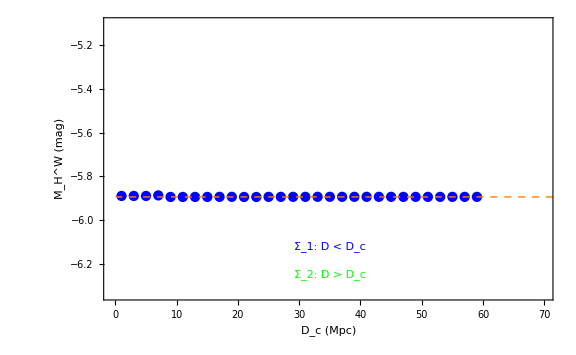
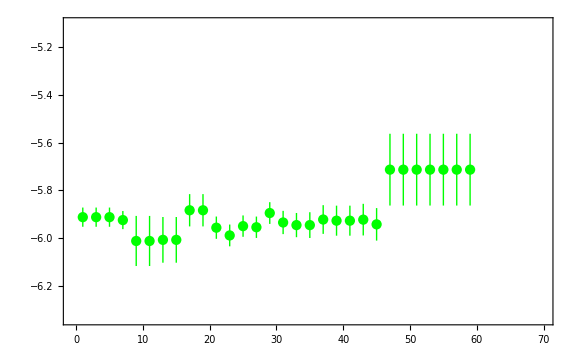
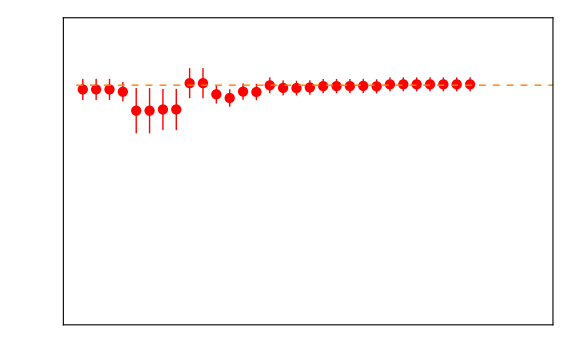

```mathematica
plh0dat={};
plparsdat={};
plparldat={};
plsdist={};
plchi2min={};
plchi2red={};
plaic={};
pldaic={};
plbic={};
pldbic={};
Do[
percol1s=percol1;
percol1l=percol1;
Do[
If[dist1[[i]]≥ dcrit,percol1s[[i]]=0]; (* in the nearby Subscript[M, H,s]^W column put 0 in the distant elements i.e. those that are beyond dcrit *)
If[0<=dist1[[i]]< dcrit,percol1l[[i]]=0] (* in the distant Subscript[M, H,l]^W column put 0 in the nearby elements i.e. those that are closer than dcrit. Elements with negative distance are ignored. *)
,{i,1,Length[dist1]}];
trL1=Drop[trL,{col}] ;(* Remove the MW column of L to replace it with two other columns for the nearby and distant parameters (Subscript[M, H,s]^W  and Subscript[M, H,l]^W) *)
trL2=Insert[Insert[trL1,percol1s,col],percol1l,col+1] ;(* Replace with the new columns *)
Lnew=Transpose[trL2]; (* this is the model matrix Lnew for the new model with one new parameter *)
trLnew=trL2 ;(* The system is Y=L qpar. qpar has single column with 47 entries. Entry 45 is useless and does not appear anywhere but we keep it for completeness as it has been included in the fits data but it is not mentioned in Riess 21. *);
sigma=Inverse[trLnew.InvCall.Lnew];
qbf=sigma.(trLnew.InvCall.Y) ;(* These are the best fit parameter values. These formulas are proven in https://people.duke.edu/~hpgavin/SystemID/CourseNotes/linear-least-squres.pdf Eq. 11 *);
(* the best fit papameter values with 1 sigma errors for H0 and for the two new parameters *)
h0=10^(qbf[[48]]/5) (* We obtain the correct value of h0 since qbf[[47]]= 5 log Subscript[H, 0]  *);
dqbf48=Sqrt[sigma[[48,48]]];
dh0=Log[10] h0 dqbf48/5 ;
vec=Y-Lnew.qbf;
chi2min=vec.InvCall.vec;
Print["Distance=",dcrit,"---------------"];
Print["H_0=",h0,"±",dh0];
dpars=Sqrt[sigma[[col,col]]];
dparl=Sqrt[sigma[[col+1,col+1]]];
pars=ToString[qpar1[[col]]];
parl=ToString[qpar1[[col+1]]];
sdist=Abs[(qbf[[col]] -qbf[[col+1]])]/(dpars ^2+dparl ^2)^0.5(* We obtain the σ-distance *);
Print[pars,"=",qbf[[col]],"±",dpars];
Print[parl,"=",qbf[[col+1]],"±",dparl];
Print["σ-distance = ",sdist];
Print["Mb","=",qbf[[44]],"±",Sqrt[sigma[[44,44]]]];
Print["Δbw","=",qbf[[43]],"±",Sqrt[sigma[[43,43]]]];
Print["Zw","=",qbf[[45]],"±",Sqrt[sigma[[45,45]]]];
Print["χ_min^2 = ",chi2min];
Print["χ_red^2 = ",chi2min/dof];
Print["AIC = ",chi2min+2*MM];
Print["ΔAIC = ",chi2min+2*MM-3646.7593303](* this is the AIC obtained from the zero order model of SH0ES (see Baseline1 file)*);
Print["BIC = ",chi2min+MM*Log[NN]];
Print["ΔBIC = ",chi2min+MM*Log[NN]-3936.1961364](* this is the BIC obtained from the zero order model of SH0ES (see Baseline1 file)*);
AppendTo[plh0dat,{dcrit,Around[h0,dh0]}];
AppendTo[plparsdat,{dcrit,Around[qbf[[col]],dpars]}];
AppendTo[plparldat,{dcrit,Around[qbf[[col+1]],dparl]}];
AppendTo[plsdist,{dcrit,sdist}];
AppendTo[plchi2min,{dcrit,chi2min}];
AppendTo[plchi2red,{dcrit,chi2min/dof}];
AppendTo[plaic,{dcrit,chi2min+2*MM}];
AppendTo[pldaic,{dcrit,chi2min+2*MM-3646.7593303}](* this is the AIC obtained from the zero order model of sh0es (see Baseline1 file)*);
AppendTo[plbic,{dcrit,chi2min+MM*Log[NN]}];
AppendTo[pldbic,{dcrit,chi2min+MM*Log[NN]-3936.1961364}](* this is the ΒIC obtained from the zero order model of sh0es (see Baseline1 file)*);
chi2min0=3552.76 (* this is the Subscript[χ, min]^2 obtained from the zero order model of SH0ES (see Baseline1 file)*);
deltachi2min=chi2min-chi2min0  (* this is the improvement of chi2min obtained by the introduction of the new parameter *),{dcrit,mindist,maxdist,step}]
data1=plparsdat;
data2=plparldat;
data3=plh0dat;
plot1=ListPlot[data1,PlotRange->{{-0.5,70},{-6.34,-5.1}},PlotStyle->Blue,ImagePadding->70,Frame->{{True,False},{True,True}},FrameStyle->Directive[{{Blue,Automatic},{Blue,Blue}},Thick],FrameLabel->{"D_c (Mpc)","M_H^W (mag)"},BaseStyle->{Large,FontFamily->"Times",18},Epilog->{{Dashing[{Small,Small}],Thickness[Medium],Orange,Line[{{0,-5.894},{80,-5.894}}]},{Blue,Inset["Σ_1: D < D_c",{35,-6.12}]},{Green,Inset["Σ_2: D > D_c",{35,-6.25}]}}];
plot2=ListPlot[data2,PlotRange->{{-0.5,70},{-6.34,-5.1}},PlotStyle->Green,ImagePadding->70,Frame->{{True,False},{True,True}},FrameStyle-> Directive[{Blue,Automatic},{Blue,Blue},Thick],BaseStyle->{Large,FontFamily->"Times",18}];
plot3=ListPlot[data3,PlotRange->{{-0.5,70},{39,82}},PlotStyle->Red,ImagePadding->70,Axes->False,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{{Automatic,Red},{Automatic,Red}},Thick],FrameLabel->{{None,"H_0 (km sec^-1 Mpc^-1)"},{None,None}},BaseStyle->{Large,FontFamily->"Times",18},Epilog->{Dashing[{Small,Small}],Thickness[Medium],Orange,Line[{{0,73.04},{80,73.04}}]}];
figmw=Overlay[Show[#,ImageSize->Large]&/@{plot1,plot2,plot3}]
```

```mathematica
Export[NotebookDirectory[]<>"figmw.pdf",figmw,ImageResolution->1000];
```

## Figures 12, 13 (Purple curves)

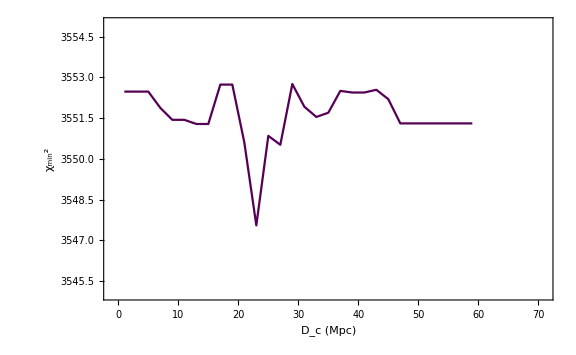

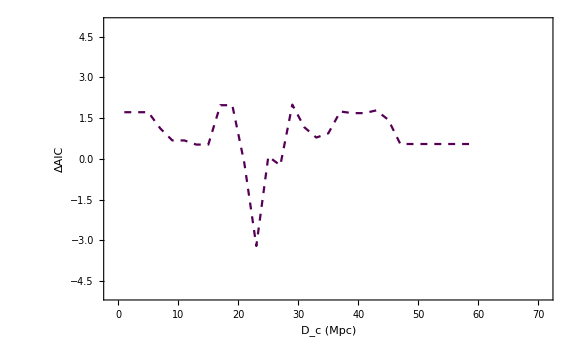

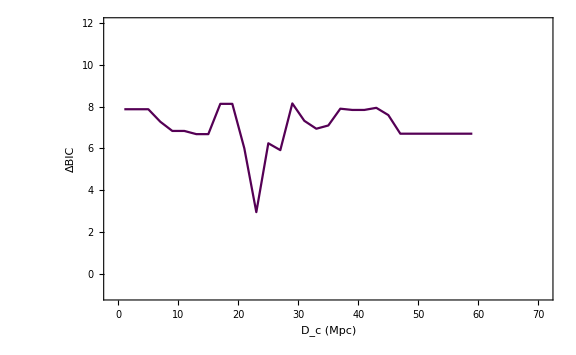

```mathematica
figsdmw=ListPlot[plsdist,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance (M_W)"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-0.5,4}},Axes->False,PlotStyle->{Darker[Purple]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the σ-distance  plot obtained from the transition model Subscript[M, W] *);
figchimw=ListPlot[plchi2min,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","χ_min^2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3545,3555}},Axes->False,PlotStyle->{Darker[Purple]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the Subscript[χ, min]^2  plot obtained from the transition model Subscript[M, W] *)

figchiredmw=ListPlot[plchi2red,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","χ_red^2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{1.0285,1.032}},Axes->False,PlotStyle->{Darker[Purple]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the Subscript[χ, red]^2  plot obtained from the transition model Subscript[M, W] *);
figaicmw=ListPlot[plaic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","AIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3642,3651}},Axes->False,PlotStyle->{Darker[Purple]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the AIC  plot obtained from the transition model Subscript[M, W] *);
figdaicmw=ListPlot[pldaic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","ΔAIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-5,5}},Axes->False,PlotStyle->{Dashed,Darker[Purple]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the ΔAIC  plot obtained from the transition model Subscript[M, W] *)
figbicmw=ListPlot[plbic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","BIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3938,3951}},Axes->False,PlotStyle->{Darker[Purple]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the BIC  plot obtained from the transition model Subscript[M, W] *);
figdbicmw=ListPlot[pldbic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","ΔBIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-1,12}},Axes->False,PlotStyle->{Darker[Purple]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the ΔBIC  plot obtained from the transition model Subscript[M, W] *)
```